```mathematica
γ[kx_,ky_]:=1/2*(Cos[kx]+Cos[ky]);
A[kx_,ky_,b_]=1+γ[kx,ky]*b^2;
B[kx_,ky_,b_]=γ[kx,ky]*(1-b^2);
ϵ[kx_,ky_,b_]=2*J*Sqrt[A[kx,ky,b]^ 2-B[kx,ky,b]^ 2]/2;
```

```mathematica
ListeNiklas={};
NNiklas=2^5;
Table[AppendTo[ListeNiklas,ϵ[kx,kx,b]],{kx,0,π,π/(NNiklas*Sqrt[2])}];
Table[AppendTo[ListeNiklas,ϵ[π-kx,π,b]],{kx,0,π,π/NNiklas}];
Table[AppendTo[ListeNiklas,ϵ[kx,π-kx,b]],{kx,0,π,π/(NNiklas*Sqrt[2])}];
Table[AppendTo[ListeNiklas,ϵ[0,π-kx,b]],{kx,0,π,π/NNiklas}];
```

```mathematica
GammaP=0+1;
MP=Ceiling[NNiklas*Sqrt[2]]+1;
XPrimeP=MP+NNiklas;
XP=XPrimeP+MP;
GammaPrimeP=XP+NNiklas;
```

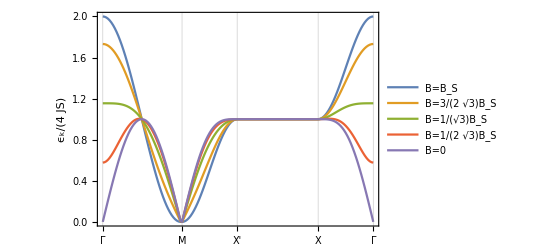

```mathematica
ListLinePlot[{ListeNiklas/.b-> 1,ListeNiklas/.b-> 3/(2Sqrt[3]),ListeNiklas/.b-> 1/Sqrt[3],ListeNiklas/.b-> 1/(2Sqrt[3]),ListeNiklas/.b-> 0},Frame->True,FrameTicks->{{Automatic,None},{{{GammaP,"Γ"},{MP,"M"},{XPrimeP,"X'"},{XP,"X"},{GammaPrimeP,"Γ"}},None}},PlotRange->{{1,GammaPrimeP},{0,2}},PlotLegends->{"B=B_S","B=3/(2 √3)B_S","B=1/(√3)B_S","B=1/(2 √3)B_S","B=0"},GridLines->{{GammaP,MP,XPrimeP,XP,GammaPrimeP},None},FrameLabel->{None,Subscript[ϵ, k]/(4JS)}]
```